(1) g1 = CycleGraph[5]

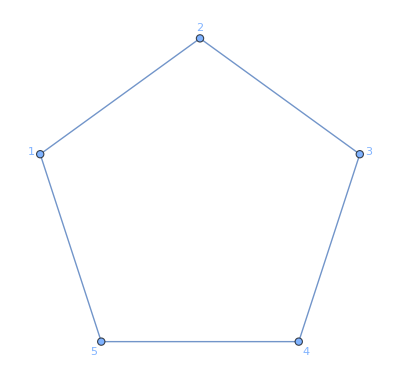

(1) g2 = TuranGraph[5, 3]

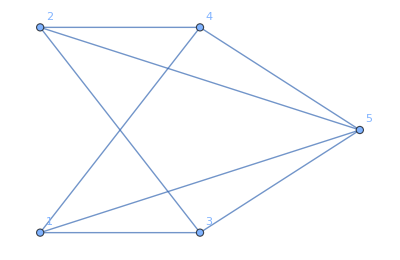

(2) g3 = GraphComplement[g1]

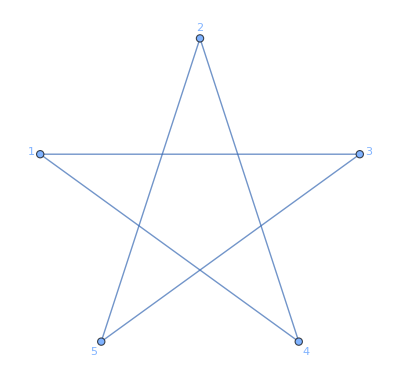

(2) g = EdgeAdd[g3, UndirectedEdge[1, 3]]

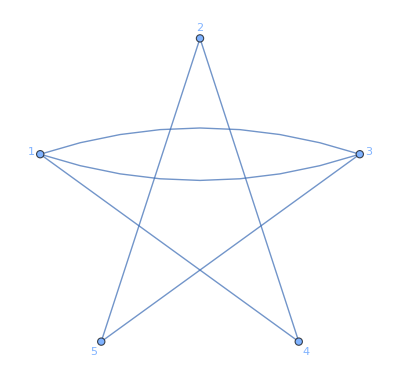

(2) g4 = StarGraph[5]

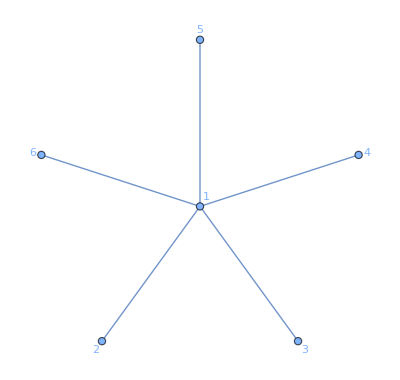

(3) GraphJoin[g1, g4]

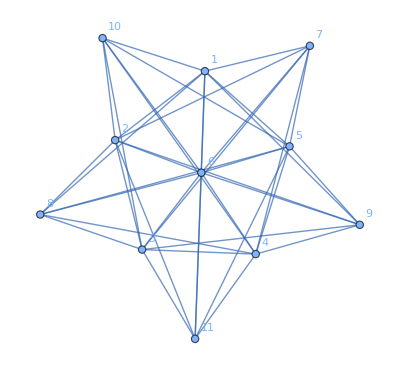

(3) compG4 = GraphComplement[g4]

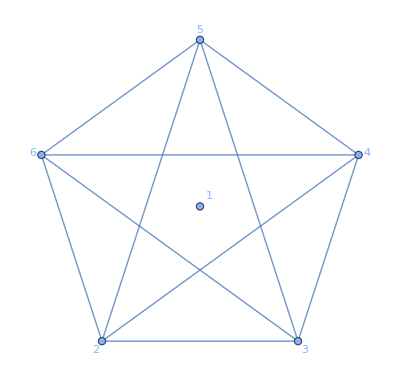

(3) diffG = GraphDifference[g1, compG4]

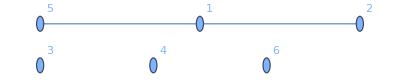

(3) interG = GraphIntersection[g4, g1]

-Graphics-

(3) prodG = GraphProduct[g4, g1]

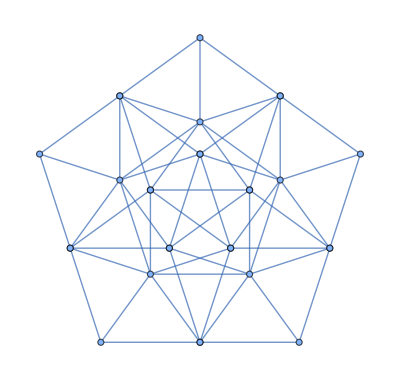

(3) sumG = GraphSum[g4, g1]

-Graphics-

(3) unionG = GraphUnion[g4, g1]

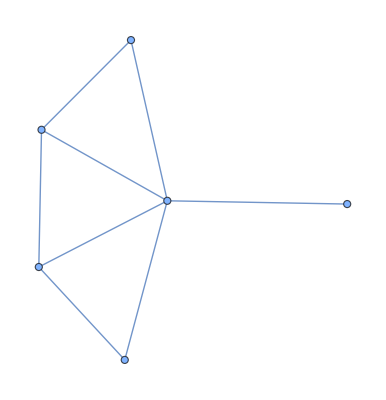

(4) g5 = AdjacencyGraph[adj]

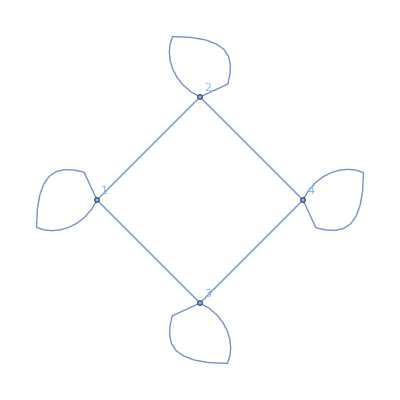

g5 is pseudo (simple)? False

SimpleGraph[g5]

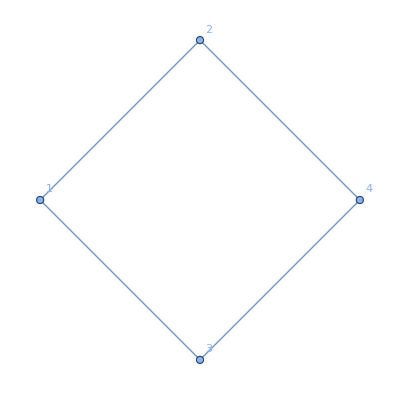

unionG2 = GraphUnion[g5, LineGraph[g3]]

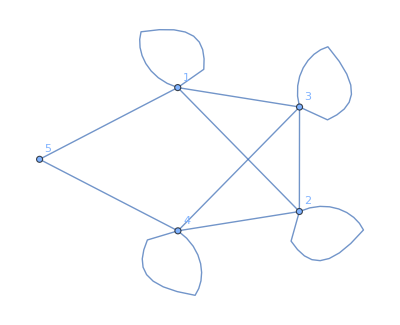

Subgraph[g5, {1, 2, 3}]

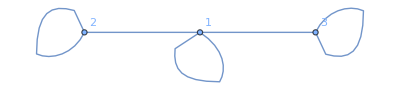

g7 = Subgraph[g5, {1, 2, 3}]

-Graphics-

Components of g5: {{1,2,3,4}}

{1,1,4,2}

```mathematica
(*1. Графы*)(*1.1 2-регулярный граф с 5 вершинами*)g1=CycleGraph[5];
Print["(1) g1 = CycleGraph[5]"];
Graph[g1,VertexLabels->"Name"]

(*1.2 Граф Турана с параметрами 5 и 3*)
g2=TuranGraph[5,3];
Print["(1) g2 = TuranGraph[5, 3]"];
Graph[g2,VertexLabels->"Name"]

(*2. Операции над графами*)

(*2.1 Дополнение (комплемент) g1*)
g3=GraphComplement[g1];
Print["(2) g3 = GraphComplement[g1]"];
Graph[g3,VertexLabels->"Name"]

(*2.2 Соединение 1 и 3 вершины в g3 и получаем g*)
g=EdgeAdd[g3,UndirectedEdge[1,3]];
Print["(2) g = EdgeAdd[g3, UndirectedEdge[1, 3]]"];
Graph[g,VertexLabels->"Name"]

(*2.3 Граф-звезда с 5 вершинами (StarGraph[n] даёт n+1 вершину)*)
g4=StarGraph[6];
Print["(2) g4 = StarGraph[5]"];
Graph[g4,VertexLabels->"Name"]

(*3. Операции над графами g1 и g4*)

(*3.1 Соединение графов (GraphJoin)*)
Print["(3) GraphJoin[g1, g4]"];
Graph[GraphJoin[g1,g4],VertexLabels->"Name"]

(*3.2 Дополнение g4*)
compG4=GraphComplement[g4];
Print["(3) compG4 = GraphComplement[g4]"];
Graph[compG4,VertexLabels->"Name"]

(*3.3 Разность графов (g1 minus комплемент g4)*)
diffG=GraphDifference[g1,compG4];
Print["(3) diffG = GraphDifference[g1, compG4]"];
Graph[diffG,VertexLabels->"Name"]

(*3.4 Пересечение g4 и g1*)
interG=GraphIntersection[g4,g1];
Print["(3) interG = GraphIntersection[g4, g1]"];
Graph[interG,VertexLabels->"Name"]

(*3.5 Произведение графов*)
prodG=GraphProduct[g4,g1];
Print["(3) prodG = GraphProduct[g4, g1]"];
Graph[prodG]

(*3.6 Сумма графов*)
sumG=GraphSum[g4,g1];
Print["(3) sumG = GraphSum[g4, g1]"];
Graph[sumG]

(*3.7 Объединение графов*)
unionG=GraphUnion[g4,g1];
Print["(3) unionG = GraphUnion[g4, g1]"];
Graph[unionG]

(*4. Граф по матрице смежности*)

adj={{1,1,1,0},{1,1,0,1},{1,0,1,1},{0,1,1,1}};
g5=AdjacencyGraph[adj,VertexLabels->"Name"];
Print["(4) g5 = AdjacencyGraph[adj]"];
Graph[g5,VertexLabels->"Name"]

(*Проверка на простоту (псевдограф?)*)
Print["g5 is pseudo (simple)? ",SimpleGraphQ[g5]]  (*FALSE-значит это псевдограф*)

(*Сделать граф простым*)
Print["SimpleGraph[g5]"];
Graph[SimpleGraph[g5],VertexLabels->"Name"]

(*Объединение графов g5 и реберного графа g3*)
unionG2=GraphUnion[g5,LineGraph[g3]];
Print["unionG2 = GraphUnion[g5, LineGraph[g3]]"];
Graph[unionG2,VertexLabels->"Name"]

(*Подграф g7 с вершинами 1,2,3*)
Print["Subgraph[g5, {1, 2, 3}]"];
Graph[Subgraph[g5,{1,2,3}],VertexLabels->"Name"]
```